-3

3

{{0,-3.},{4,-2.2},{8,-1.4},{12,-0.6},{16,0.2},{20,1.},{24,1.8},{28,2.6}}

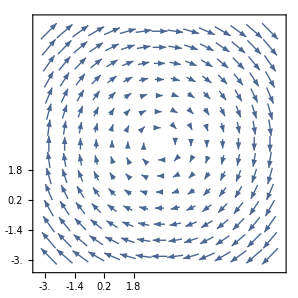

```mathematica
min = -3
max = 3

tickSpecification = Table[{i,(i * 0.2 - 3)}, {i, 0, 30, 4}]
ListVectorPlot[
Table[
{y,-x},
{x,min,max,0.1},
{y,min,max,0.1}],
FrameTicks->{{tickSpecification, None},{tickSpecification, None}},

]
```

```mathematica
Points = Import["/home/koritskiy/rqc/ferrimagnet/crit_fields_0.33-0.35.dat"]
```

{{0.33,90071.},{0.3301,90188.},{0.3302,90305.},{0.3303,90422.},{0.3304,90540.},{0.3305,90658.},{0.3306,90775.},{0.3307,90893.},{0.3308,91012.},{0.3309,91130.},{0.331,91249.},{0.3311,91367.},{0.3312,91486.},{0.3313,91605.},{0.3314,91724.},{0.3315,91844.},{0.3316,91963.},{0.3317,92083.},{0.3318,92203.},{0.3319,92323.},{0.332,92443.},{0.3321,92564.},{0.3322,92684.},{0.3323,92805.},{0.3324,92926.},{0.3325,93047.},{0.3326,93169.},{0.3327,93290.},{0.3328,93412.},{0.3329,93534.},{0.333,93656.},{0.3331,93778.},{0.3332,93900.},{0.3333,94023.},{0.3334,94145.},{0.3335,94268.},{0.3336,94391.},{0.3337,94515.},{0.3338,94638.},{0.3339,94761.},{0.334,94885.},{0.3341,95009.},{0.3342,95133.},{0.3343,95257.},{0.3344,95382.},{0.3345,87504.},{0.3345,87505.},{0.3345,95507.},{0.3346,87400.},{0.3346,87404.},{0.3346,88909.},{0.3346,90503.},{0.3346,95631.},{0.3347,87294.},{0.3347,87303.},{0.3347,88186.},{0.3347,91348.},{0.3347,95756.},{0.3348,87185.},{0.3348,87202.},{0.3348,87745.},{0.3348,91914.},{0.3348,95881.},{0.3349,87074.},{0.3349,87101.},{0.3349,87409.},{0.3349,92377.},{0.3349,96007.},{0.335,86958.},{0.335,87001.},{0.335,87136.},{0.335,92782.},{0.335,96132.},{0.3351,86837.},{0.3351,86900.},{0.3351,86907.},{0.3351,93148.},{0.3351,96258.},{0.3352,86708.},{0.3352,86715.},{0.3352,86800.},{0.3352,93486.},{0.3352,96384.},{0.3353,86699.},{0.3353,93801.},{0.3353,96510.},{0.3354,86599.},{0.3354,94099.},{0.3354,96636.},{0.3355,86499.},{0.3355,94383.},{0.3355,96762.},{0.3356,86399.},{0.3356,94654.},{0.3356,96889.},{0.3357,86299.},{0.3357,94915.},{0.3357,97016.},{0.3358,86199.},{0.3358,95166.},{0.3358,97143.},{0.3359,86100.},{0.3359,95410.},{0.3359,97270.},{0.336,86000.},{0.336,95646.},{0.336,97397.},{0.3361,85901.},{0.3361,95876.},{0.3361,97524.},{0.3362,85801.},{0.3362,96100.},{0.3362,97652.},{0.3363,85702.},{0.3363,96319.},{0.3363,97780.},{0.3364,85603.},{0.3364,96533.},{0.3364,97908.},{0.3365,85504.},{0.3365,96742.},{0.3365,98036.},{0.3366,85405.},{0.3366,96948.},{0.3366,98164.},{0.3367,85306.},{0.3367,97149.},{0.3367,98293.},{0.3368,85208.},{0.3368,97347.},{0.3368,98421.},{0.3369,85109.},{0.3369,97542.},{0.3369,98550.},{0.337,85011.},{0.337,97733.},{0.337,98679.},{0.3371,84912.},{0.3371,97922.},{0.3371,98808.},{0.3372,84814.},{0.3372,98108.},{0.3372,98938.},{0.3373,84716.},{0.3373,98291.},{0.3373,99067.},{0.3374,84618.},{0.3374,98472.},{0.3374,99197.},{0.3375,84520.},{0.3375,98651.},{0.3375,99327.},{0.3376,84422.},{0.3376,98827.},{0.3376,99457.},{0.3377,84324.},{0.3377,99001.},{0.3377,99587.},{0.3378,84227.},{0.3378,99173.},{0.3378,99718.},{0.3379,84129.},{0.3379,99344.},{0.3379,99848.},{0.338,84032.},{0.338,99512.},{0.338,99979.},{0.3381,83935.},{0.3381,99679.},{0.3381,100110.},{0.3382,83838.},{0.3382,99844.},{0.3382,100241.},{0.3383,83740.},{0.3383,100008.},{0.3383,100373.},{0.3384,83644.},{0.3384,100170.},{0.3384,100504.},{0.3385,83547.},{0.3385,100330.},{0.3385,100636.},{0.3386,83450.},{0.3386,100489.},{0.3386,100768.},{0.3387,83353.},{0.3387,100647.},{0.3387,100900.},{0.3388,83257.},{0.3388,100803.},{0.3388,101032.},{0.3389,83160.},{0.3389,100959.},{0.3389,101164.},{0.339,83064.},{0.339,101113.},{0.339,101297.},{0.3391,82968.},{0.3391,101265.},{0.3391,101430.},{0.3392,82872.},{0.3392,101417.},{0.3392,101563.},{0.3393,82776.},{0.3393,101568.},{0.3393,101696.},{0.3394,82680.},{0.3394,101717.},{0.3394,101829.},{0.3395,82584.},{0.3395,101865.},{0.3395,101963.},{0.3396,82489.},{0.3396,102013.},{0.3396,102096.},{0.3397,82393.},{0.3397,102159.},{0.3397,102230.},{0.3398,82298.},{0.3398,102305.},{0.3398,102364.},{0.3399,82203.},{0.3399,102449.},{0.3399,102498.},{0.34,82107.},{0.34,102593.},{0.34,102633.},{0.3401,82012.},{0.3401,102736.},{0.3401,102767.},{0.3402,81917.},{0.3402,102878.},{0.3402,102902.},{0.3403,81822.},{0.3403,103019.},{0.3403,103037.},{0.3404,81728.},{0.3404,103159.},{0.3404,103172.},{0.3405,81633.},{0.3405,103299.},{0.3405,103307.},{0.3406,81538.},{0.3406,103438.},{0.3406,103443.},{0.3407,81444.},{0.3407,103576.},{0.3407,103578.},{0.3408,81350.},{0.3408,103713.},{0.3408,103714.},{0.3409,81256.},{0.341,81161.},{0.3411,81067.},{0.3412,80974.},{0.3413,80880.},{0.3414,80786.},{0.3415,80693.},{0.3416,80599.},{0.3417,80506.},{0.3418,80413.},{0.3419,80320.},{0.342,80227.},{0.3421,80134.},{0.3422,80041.}}

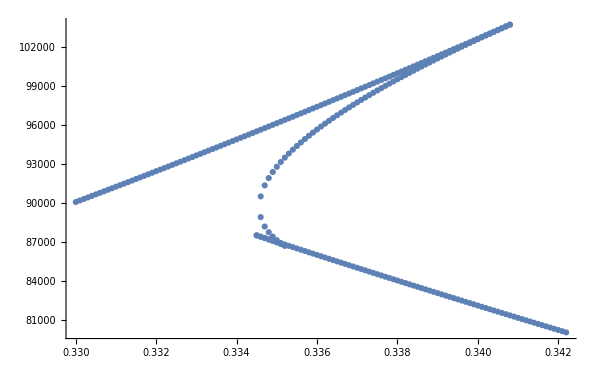

```mathematica
buckling = ListPlot[Points]
```

```mathematica
Plot[290000*Sin[x], {x,0.33,0.34}]
```

```mathematica
5
```

5

```mathematica
a = %
```

5

```mathematica
a
```

5